```mathematica
ClearAll
data=Import["/Volumes/tianjie 1/code/research/panglin_prj/data_sl.csv","CSV"];
```

ClearAll

```mathematica
xData=data[[All,1]];
yData=data[[All,2]];


model = a*x^2 +b*x+c;
fit = FindFit[Transpose[{xData,yData}],model,{a,b,c},x];

f = model/.fit
```

31.736-37.9152 x+11.6806 x^2

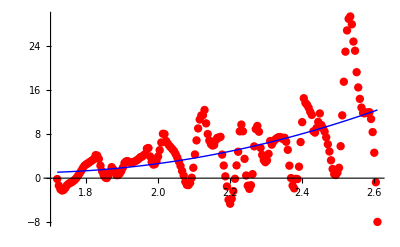

```mathematica
(*绘制数据点*)dataPlot=ListPlot[Transpose[{xData,yData}],PlotStyle->{PointSize[0.015],Red}];

(*绘制拟合线*)
ModelPlot=Plot[f,{x,Min[xData],Max[xData]},PlotStyle->{Thick,Blue}];

(*显示数据点和拟合线*)
Show[dataPlot,ModelPlot]
```